```mathematica
<<IGraphM`

IGVersion[]
```

```mathematica
EvenKneserGirth[n_,r_]:=If[n==2r+1,6,4]
OddKneserGirth[n_,r_]:=2Ceiling[r/(n-2r)]+1
```

```mathematica
WSLImport[filename_]:=IGImport["C:\\Users\\Davin Park\\AppData\\Local\\Packages\\CanonicalGroupLimited.UbuntuonWindows_79rhkp1fndgsc\\LocalState\\rootfs\\home\\dpark3542\\"<>filename<>".g6"]
```

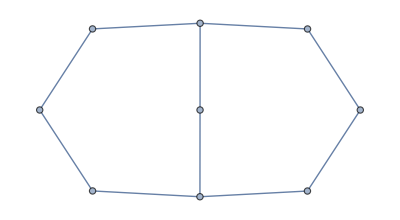
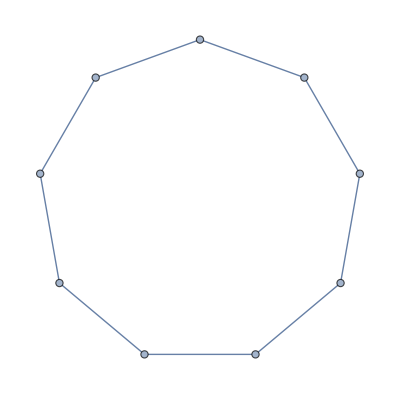

```mathematica
Select[WSLImport["graph9"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%
```

{5,4}

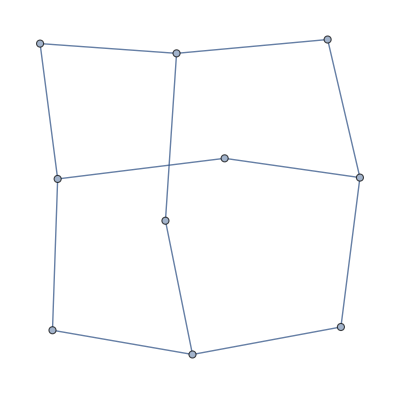
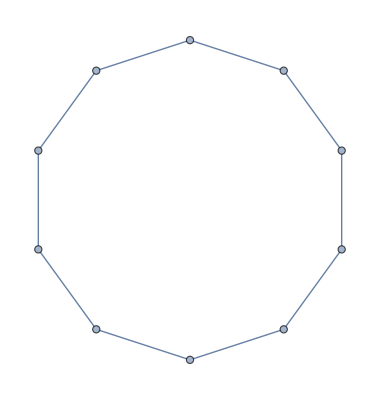
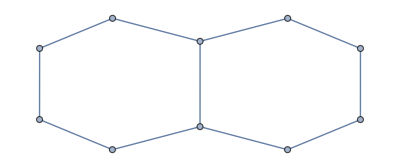

```mathematica
Select[WSLImport["graph10"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%
```

{6,5,5}

```mathematica
5*10-2Max[EdgeCount/@%92]
```

26

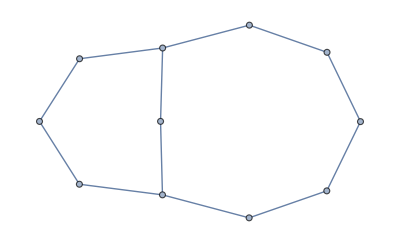
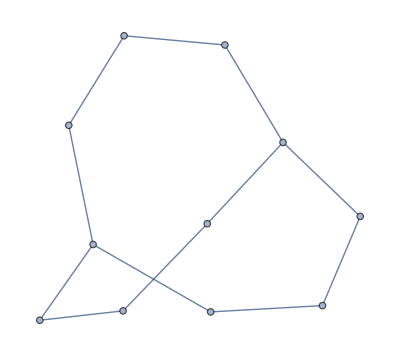
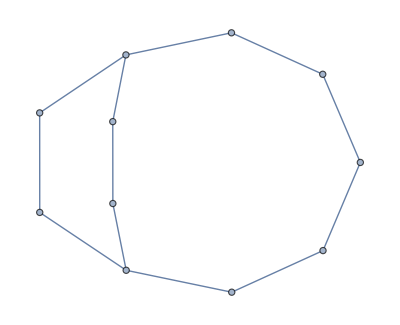
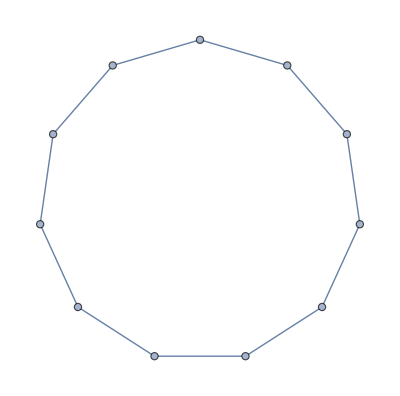

```mathematica
Select[WSLImport["graph11"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%
```

{6,6,5,5}

```mathematica
5*11-2Max[EdgeCount/@%94]
```

31

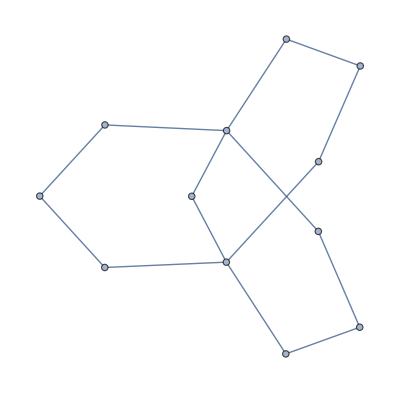
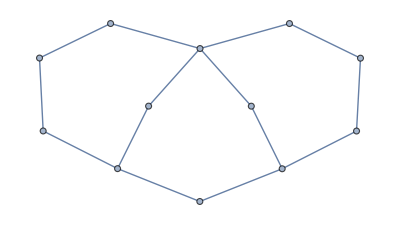
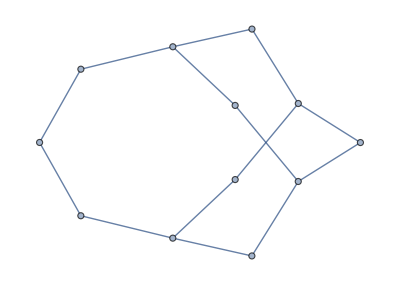
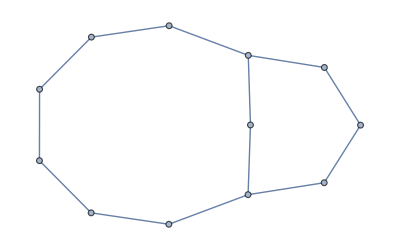
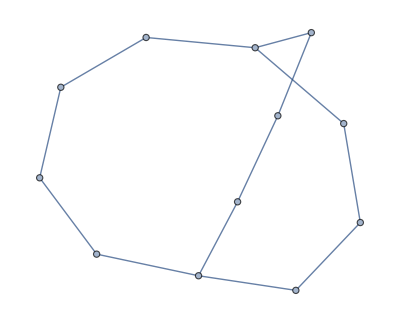
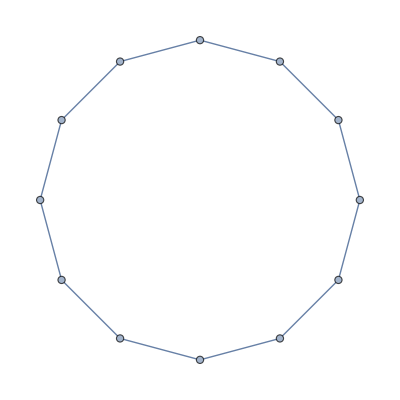
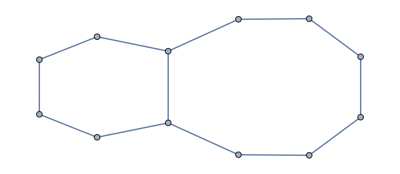
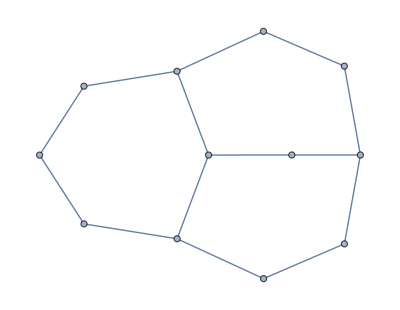

```mathematica
Select[WSLImport["graph12"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%96
```

{7,7,7,6,6,6,6,6,6,6,6}

```mathematica
5*12-2Max[EdgeCount/@%96]
```

32

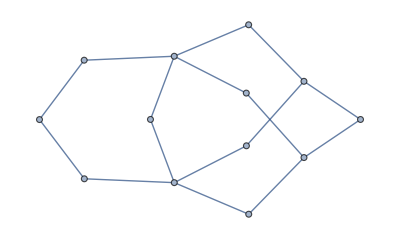
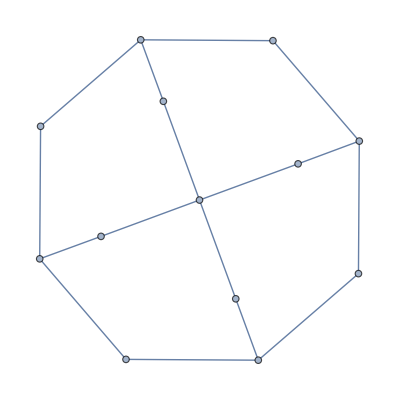
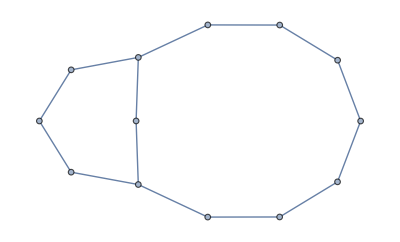
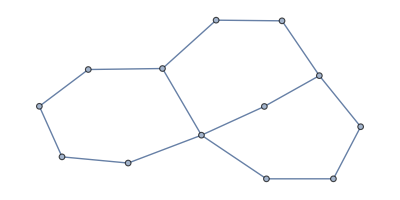
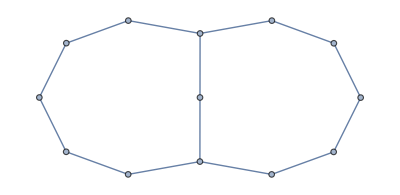
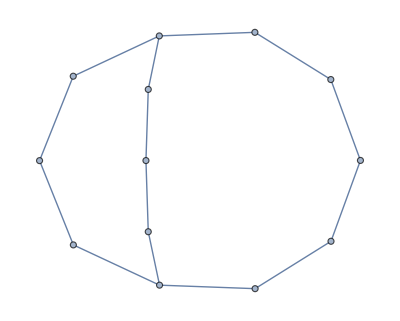
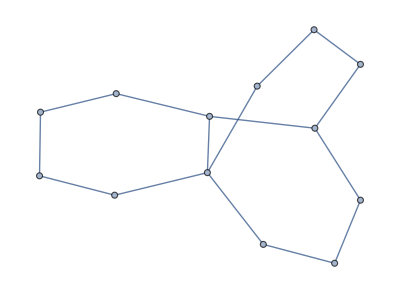
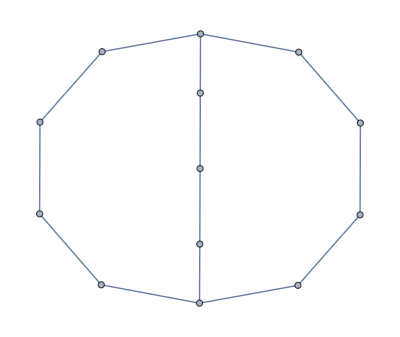

```mathematica
Select[WSLImport["graph13"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%
```

{8,8,7,7,7,7,7,6,6,6,6,6,7,6,6,6,7,7,6,6}

```mathematica
5*13-2Max[EdgeCount/@%105]
```

33

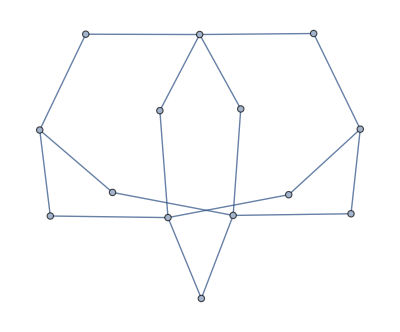
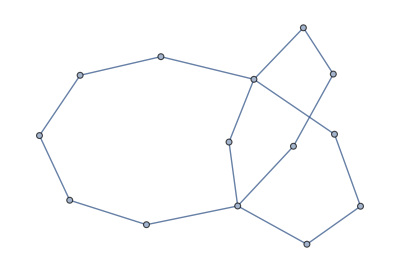
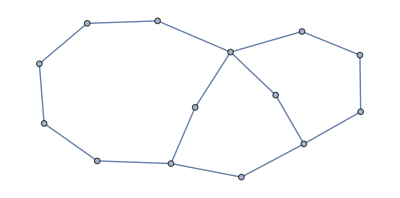
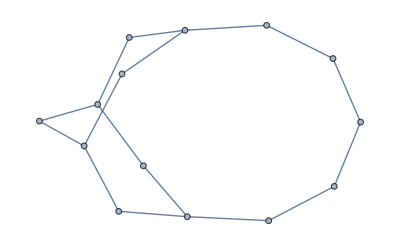
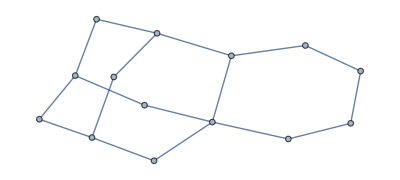
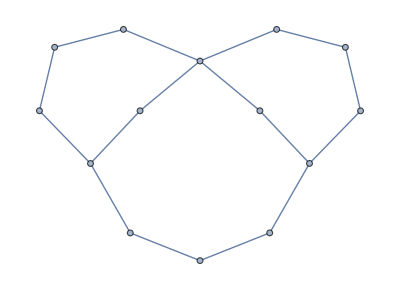
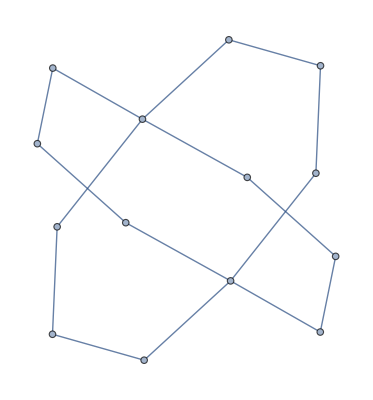
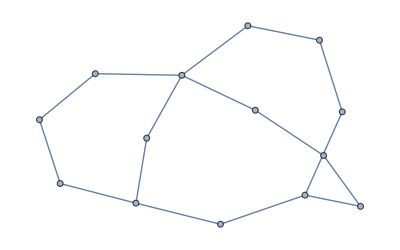

```mathematica
Select[WSLImport["graph14"],Length@FindCycle[#,5,1]==0&&Length@FindCycle[#,{7},1]==0&&IGLADSubisomorphicQ[#,KneserGraph[9,4],"Induced"->True]&]
```

```mathematica
Length@First@FindIndependentVertexSet[#,Infinity,1]&/@%
```

{9,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

```mathematica
5*14-2Max[EdgeCount/@%109]
```

34

```mathematica
s=Import["C:\\Users\\Davin Park\\AppData\\Local\\Packages\\CanonicalGroupLimited.UbuntuonWindows_79rhkp1fndgsc\\LocalState\\rootfs\\home\\dpark3542\\graph"<>ToString[17]<>".g6","Text"];
```

```mathematica
t=StringSplit[s];
```

```mathematica
Length[t]
```

35134823

```mathematica
m=0;
```

```mathematica
g=None;
```

```mathematica
Do[g=IGFromNauty[t⟦i⟧];If[m<EdgeCount[g]&&FindCycle[g,{5}]=={}&&FindCycle[g,{7}]=={},m=EdgeCount[g]];If[Divisible[i,351348],Print[i/351348]],{i,1,Length[t]}]
```

```mathematica
m
```

26

```mathematica
5*17-2*26
```

33

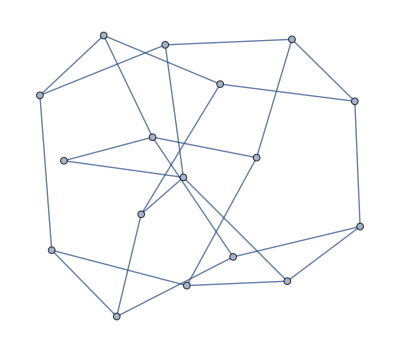
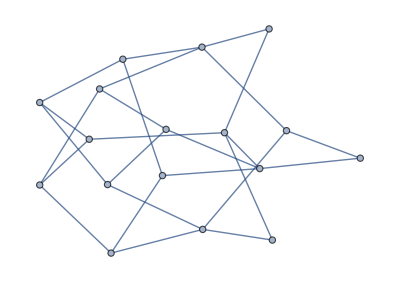
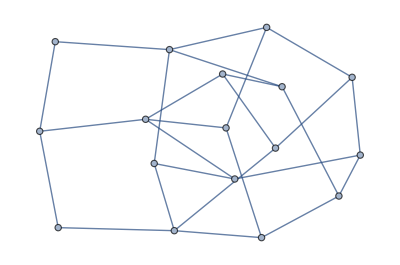
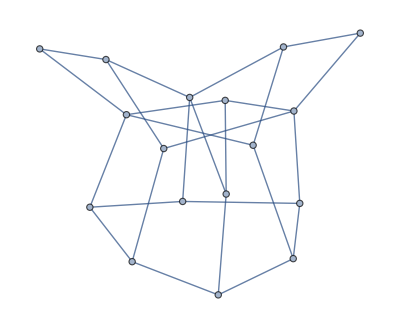

```mathematica
Select[IGImportString["P??????wCoOoSOHO@WAX?Kg?
P????A?W?o?wT?J?UOEQ??N?
P????B?K?W?Wi?U?KoCi??N?
P????B?K?W?Wi?W_QoAq??N?","Graph6"],FindCycle[#,5]=={}&&FindCycle[#,{7}]=={}&]
```

```mathematica
FindIndependentVertexSet/@%
```

{{{1,2,3,4,5,6,7,8,9}},{{1,2,3,4,5,6,7,8,17}},{{1,2,3,4,5,6,7,8,17}},{{1,2,3,4,5,6,7,8,17}}}

```mathematica
Length[First[#]]&/@%
```

{9,9,9,9}

```mathematica
9+9+35
```

53

```mathematica
s=Import["C:\\Users\\Davin Park\\AppData\\Local\\Packages\\CanonicalGroupLimited.UbuntuonWindows_79rhkp1fndgsc\\LocalState\\rootfs\\home\\dpark3542\\test2.g6","Text"];
```

```mathematica
Select[StringSplit[s],FindCycle[IGFromNauty[#],{7}]=={}&,5]
```

{P????A?O@?A?a?@_@gBa??n?,P????A?O@?A?a?@_@gBd?_V?,P????A?O@?A?B?o_EG?R_@b?,P????A?O@?A?B?o_@M@k??RO,P????A?O@?A?B?A_OGBi??n?}

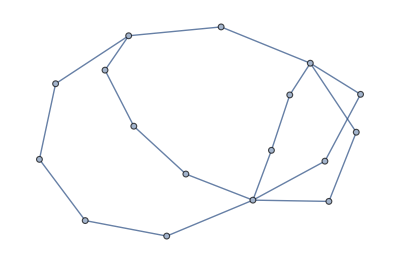
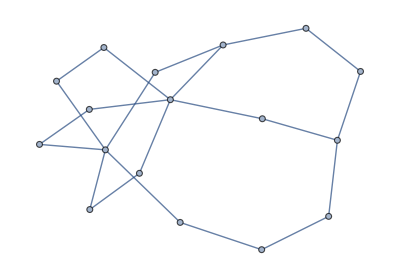
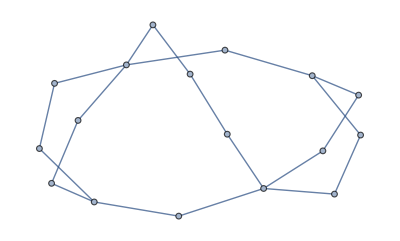
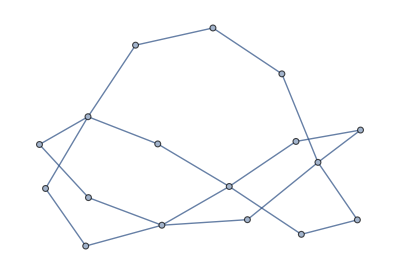
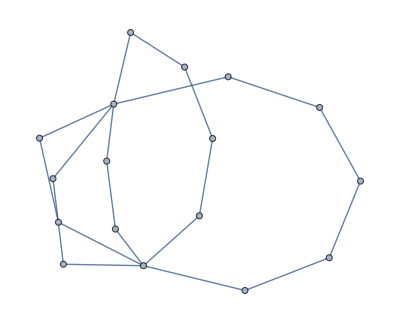

```mathematica
IGFromNauty/@%
```

```mathematica
IGLADGetSubisomorphism[%32⟦3⟧,KneserGraph[9,4],"Induced"->True]
```

{<|1→{1,2,3,4},2→{2,3,4,6},3→{3,6,7,9},4→{1,3,7,9},5→{1,6,7,8},6→{1,2,6,8},7→{1,2,4,6},8→{1,6,7,9},9→{6,7,8,9},10→{1,7,8,9},11→{1,2,4,8},12→{2,4,6,8},13→{3,4,5,9},14→{5,7,8,9},15→{2,4,5,8},16→{2,3,4,5},17→{3,5,7,9}|>}

```mathematica
Values[%]
```

{{{1,2,3,4},{2,3,4,6},{3,6,7,9},{1,3,7,9},{1,6,7,8},{1,2,6,8},{1,2,4,6},{1,6,7,9},{6,7,8,9},{1,7,8,9},{1,2,4,8},{2,4,6,8},{3,4,5,9},{5,7,8,9},{2,4,5,8},{2,3,4,5},{3,5,7,9}}}

```mathematica
Subgraph[KneserGraph[9,4],First[%]]
```

-Graphics-

```mathematica
FindIndependentVertexSet[%41]
```

{{{1,2,3,4},{2,3,4,6},{3,6,7,9},{1,3,7,9},{1,6,7,8},{1,2,6,8},{1,2,4,6},{1,6,7,9}}}

```mathematica
Table[Solve[5t-2e==f[9,4,t]],{t,6,17}]
```

{{{e→6}},{{e→7}},{{e→9}},{{e→10}},{{e→12}},{{e→14}},{{e→16}},{{e→18}},{{e→21}},{{e→22}},{{e→24}},{{e→26}}}